```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory:,",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory:,",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list:",runNum={10210,10219,10224,10227,10231,10239,10246,10261,10262,10264,10265,10270,10271,10273,10276,10281,10284,10286,10297,10345,10353,10357,10358,10386,10390,10391,10400,10404,10413,10415,10417,10420,10450,10451,10453,10455,10462,10463,10465,10469,10471,10472,10476,10483,10497,10541}]
(*2016:{11149,11154,11159,11162,11166,11170,11205,11208,11213,11214,11218,11219,11239,11243,11247,11250,11255,11263,11267,11270,11272,11276,11277,11281,11289,11292,11295,11299,11305,11325,11331,11334,11342,11348,11351,11354,11357,11360,11363,11366,11385,11388,11391,11395,11398,11399,11402,11405,11406,11409,11412,11416,11430,11433,11436,11439,11442,11445,11448,11453,11457,11461,11464},
{11149,11154,11159,11162,11166,11170,11205,11213,11214,11218,11219,11239,11243,11247,11250,11255,11263,11267,11270,11272,11276,11277,11281,11289,11292,11295,11299,11305,11325,11334,11342,11348,11351,11354,11360,11363,11366,11385,11388,11391,11395,11398,11399,11402,11405,11406,11409,11412,11416,11430,11433,11436,11439,11442,11445,11448,11453,11457,11461,11464},
2015:{10210,10219,10224,10227,10231,10239,10246,10261,10262,10264,10265,10270,10271,10273,10276,10281,10284,10286,10297,10345,10353,10357,10358,10386,10390,10391,10400,10404,10413,10415,10417,10420,10450,10451,10453,10455,10462,10463,10465,10469,10471,10472,10476,10483,10497,10541}]*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=4;binw=10;
histbeg2=0;
ptreal=Table[0,{k,1,runn}];
ptdat=0;
ptdat2=0;
```

Working Directory:,C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory:,C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list:{10210,10219,10224,10227,10231,10239,10246,10261,10262,10264,10265,10270,10271,10273,10276,10281,10284,10286,10297,10345,10353,10357,10358,10386,10390,10391,10400,10404,10413,10415,10417,10420,10450,10451,10453,10455,10462,10463,10465,10469,10471,10472,10476,10483,10497,10541}

#Runs in the list: 46

```mathematica
For[runi=1,runi≤runn,runi++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Run #",runNum[[runi]]];
Print["Size of event list in Cycle: ",dimdata=Dimensions[data][[1]]];
histdata=HistogramList[data[[1;;dimdata,6]],{histbeg,histlast,binw}];
histdata2=HistogramList[data[[1;;dimdata,5]],{histbeg2,histlast,binw}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
ptdat2=Table[{0,0},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=13.6*(histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[i]][[2]]=histdata[[2]][[i]];
];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[i]][[1]]=13.6*(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2));
ptdat2[[i]][[2]]=histdata2[[2]][[i]];
];
Print["Number of events in run #",runNum[[runi]],": ",Total[histdata[[2]]]];
ptreal[[runi]]=ListLinePlot[{ptdat,ptdat2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","N(#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->IntegerString[runNum[[runi]],10,6],Filling->Axis,ImageSize->{300}];
Print["--------------------------------------------"];
];
runi--;
```

Run #10210

Size of event list in Cycle: 353576

Number of events in run #10210: 353531

--------------------------------------------

Run #10219

Size of event list in Cycle: 540478

Number of events in run #10219: 540410

--------------------------------------------

Run #10224

Size of event list in Cycle: 578026

Number of events in run #10224: 577953

--------------------------------------------

Run #10227

Size of event list in Cycle: 411812

Number of events in run #10227: 411751

--------------------------------------------

Run #10231

Size of event list in Cycle: 606872

Number of events in run #10231: 606788

--------------------------------------------

Run #10239

Size of event list in Cycle: 514687

Number of events in run #10239: 514622

--------------------------------------------

Run #10246

Size of event list in Cycle: 639150

Number of events in run #10246: 639061

--------------------------------------------

Run #10261

Size of event list in Cycle: 609074

Number of events in run #10261: 608983

--------------------------------------------

Run #10262

Size of event list in Cycle: 570079

Number of events in run #10262: 569988

--------------------------------------------

Run #10264

Size of event list in Cycle: 464758

Number of events in run #10264: 464706

--------------------------------------------

Run #10265

Size of event list in Cycle: 426382

Number of events in run #10265: 426335

--------------------------------------------

Run #10270

Size of event list in Cycle: 612032

Number of events in run #10270: 611942

--------------------------------------------

Run #10271

Size of event list in Cycle: 544600

Number of events in run #10271: 544525

--------------------------------------------

Run #10273

Size of event list in Cycle: 627802

Number of events in run #10273: 627709

--------------------------------------------

Run #10276

Size of event list in Cycle: 649757

Number of events in run #10276: 649675

--------------------------------------------

Run #10281

Size of event list in Cycle: 602995

Number of events in run #10281: 602904

--------------------------------------------

Run #10284

Size of event list in Cycle: 478755

Number of events in run #10284: 478698

--------------------------------------------

Run #10286

Size of event list in Cycle: 656264

Number of events in run #10286: 656177

--------------------------------------------

Run #10297

Size of event list in Cycle: 163321

Number of events in run #10297: 163302

--------------------------------------------

Run #10345

Size of event list in Cycle: 475288

Number of events in run #10345: 475234

--------------------------------------------

Run #10353

Size of event list in Cycle: 381841

Number of events in run #10353: 381788

--------------------------------------------

Run #10357

Size of event list in Cycle: 346591

Number of events in run #10357: 346544

--------------------------------------------

Run #10358

Size of event list in Cycle: 296542

Number of events in run #10358: 296505

--------------------------------------------

Run #10386

Size of event list in Cycle: 474601

Number of events in run #10386: 474544

--------------------------------------------

Run #10390

Size of event list in Cycle: 517815

Number of events in run #10390: 517734

--------------------------------------------

Run #10391

Size of event list in Cycle: 469653

Number of events in run #10391: 469597

--------------------------------------------

Run #10400

Size of event list in Cycle: 234354

Number of events in run #10400: 234311

--------------------------------------------

Run #10404

Size of event list in Cycle: 397166

Number of events in run #10404: 397116

--------------------------------------------

Run #10413

Size of event list in Cycle: 582396

Number of events in run #10413: 582329

--------------------------------------------

Run #10415

Size of event list in Cycle: 505934

Number of events in run #10415: 505865

--------------------------------------------

Run #10417

Size of event list in Cycle: 616418

Number of events in run #10417: 616316

--------------------------------------------

Run #10420

Size of event list in Cycle: 635562

Number of events in run #10420: 635486

--------------------------------------------

Run #10450

Size of event list in Cycle: 516075

Number of events in run #10450: 515991

--------------------------------------------

Run #10451

Size of event list in Cycle: 557226

Number of events in run #10451: 557151

--------------------------------------------

Run #10453

Size of event list in Cycle: 484241

Number of events in run #10453: 484193

--------------------------------------------

Run #10455

Size of event list in Cycle: 369085

Number of events in run #10455: 369035

--------------------------------------------

Run #10462

Size of event list in Cycle: 653516

Number of events in run #10462: 653409

--------------------------------------------

Run #10463

Size of event list in Cycle: 623057

Number of events in run #10463: 622978

--------------------------------------------

Run #10465

Size of event list in Cycle: 373728

Number of events in run #10465: 373670

--------------------------------------------

Run #10469

Size of event list in Cycle: 677974

Number of events in run #10469: 677880

--------------------------------------------

Run #10471

Size of event list in Cycle: 574687

Number of events in run #10471: 574623

--------------------------------------------

Run #10472

Size of event list in Cycle: 377133

Number of events in run #10472: 377096

--------------------------------------------

Run #10476

Size of event list in Cycle: 702690

Number of events in run #10476: 702594

--------------------------------------------

Run #10483

Size of event list in Cycle: 482471

Number of events in run #10483: 482411

--------------------------------------------

Run #10497

Size of event list in Cycle: 684002

Number of events in run #10497: 683903

--------------------------------------------

Run #10541

Size of event list in Cycle: 775141

Number of events in run #10541: 774980

--------------------------------------------

```mathematica
width=6;
Export["2015_QDC_Monitor.png",GraphicsGrid[ArrayReshape[ptreal,{Ceiling[runn/width],width}]]]
```

2015_QDC_Monitor.png

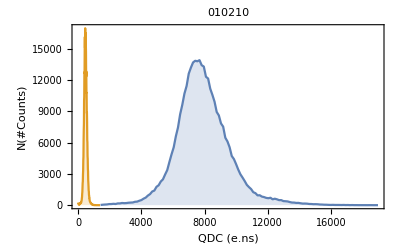

```mathematica
ptreal[[1]]
```

```mathematica
GraphicsGrid[ArrayReshape[ptreal,{Ceiling[runn/width],width}]]
```